```mathematica
FileExport[data_, filename_?StringQ, parser_?StringQ] :=
With[
{folder=FileNameJoin[{ParentDirectory@NotebookDirectory[], "LaTeX", "pic"}]},
If[FileType[folder]== None,CreateDirectory[folder]];
Export[FileNameJoin[{folder,filename}] , data, parser];
];
```

```mathematica
NN={(1-z)^2(1+2z),z(1-z)^2,z^2(3-2z),z^2(z-1)}
```

{(1-z)^2 (1+2 z),(1-z)^2 z,(3-2 z) z^2,(-1+z) z^2}

```mathematica
leg={"N_1(z)","N_2(z)","N_3(z)","N_4(z)"}
```

{N_1(z),N_2(z),N_3(z),N_4(z)}

```mathematica
Legended[NN[[#]],leg[[#]]]&/@Range[4]
```

{(1-z)^2 (1+2 z),(1-z)^2 z,(3-2 z) z^2,(-1+z) z^2}

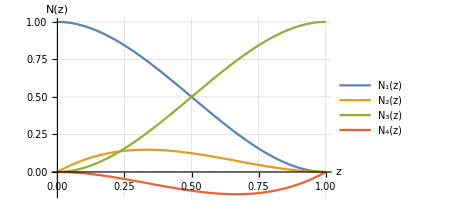

```mathematica
fig=Plot[Evaluate[Legended[NN[[#]],leg[[#]]]&/@Range[4]],{z,0,1},AxesStyle->Directive[Black,18,FontFamily->"Times"],GridLines->Automatic,AxesLabel->{"z","N(z)"},ImageSize->350]
FileExport[fig, "2_formfunctions.pdf", "PDF"]
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/arsenytokarev/Desktop/Кур/Code

```mathematica
Export["hermiteVar.pdf",fig]
```

hermiteVar.pdf

```mathematica
nn={1-23 z^2+66 z^3-68 z^4+24 z^5,z-6 z^2+13 z^3-12 z^4+4 z^5,16 z^2-32 z^3+16 z^4,-8 z^2+32 z^3-40 z^4+16 z^5,7 z^2-34 z^3+52 z^4-24 z^5,-z^2+5 z^3-8 z^4+4 z^5}
```

{1-23 z^2+66 z^3-68 z^4+24 z^5,z-6 z^2+13 z^3-12 z^4+4 z^5,16 z^2-32 z^3+16 z^4,-8 z^2+32 z^3-40 z^4+16 z^5,7 z^2-34 z^3+52 z^4-24 z^5,-z^2+5 z^3-8 z^4+4 z^5}

```mathematica
legends={"N_1(z)","N_2(z)","N_3(z)","N_4(z)","N_5(z)","N_6(z)"}
```

{N_1(z),N_2(z),N_3(z),N_4(z),N_5(z),N_6(z)}

```mathematica
Legended[nn[[#]],legends[[#]]]&/@Range[6]
```

{1-23 z^2+66 z^3-68 z^4+24 z^5,z-6 z^2+13 z^3-12 z^4+4 z^5,16 z^2-32 z^3+16 z^4,-8 z^2+32 z^3-40 z^4+16 z^5,7 z^2-34 z^3+52 z^4-24 z^5,-z^2+5 z^3-8 z^4+4 z^5}

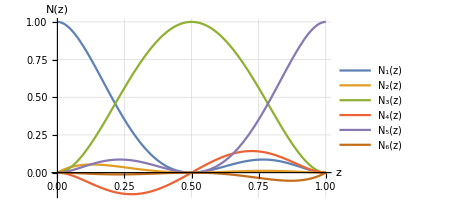

```mathematica
figure=Plot[Evaluate[Legended[nn[[#]],legends[[#]]]&/@Range[6]],{z,0,1},AxesStyle->Directive[Black,18,FontFamily->"Times"],GridLines->Automatic,AxesLabel->{"z","N(z)"},ImageSize->350]
FileExport[figure, "3_formfunctions.pdf", "PDF"]
```